```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar = RSS;
Hstar = HSS;
Fstar =FSS;
JacSpec = {
{D[dF,F],D[dF,H],D[dF,R]},
{D[dH,F],D[dH,H],D[dH,R]},
{D[dR,F],D[dR,H],D[dR,R]}
};
JacSpecSol = JacSpec/.{R->RSS,H->HSS,F->FSS};
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
(*Can't use analytic version because solution to Hopf must be numerically obtained*)
(*HopfAnalytic = Solve[Det[Sylv]==0,ρ];*)
```

```mathematica
RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,65}]
```

{1.×10^-8,1.2×10^-8,1.44×10^-8,1.728×10^-8,2.0736×10^-8,2.48832×10^-8,2.98598×10^-8,3.58318×10^-8,4.29982×10^-8,5.15978×10^-8,6.19174×10^-8,7.43008×10^-8,8.9161×10^-8,1.06993×10^-7,1.28392×10^-7,1.5407×10^-7,1.84884×10^-7,2.21861×10^-7,2.66233×10^-7,3.1948×10^-7,3.83376×10^-7,4.60051×10^-7,5.52061×10^-7,6.62474×10^-7,7.94968×10^-7,9.53962×10^-7,1.14475×10^-6,1.37371×10^-6,1.64845×10^-6,1.97814×10^-6,2.37376×10^-6,2.84852×10^-6,3.41822×10^-6,4.10186×10^-6,4.92224×10^-6,5.90668×10^-6,7.08802×10^-6,8.50562×10^-6,0.0000102067,0.0000122481,0.0000146977,0.0000176373,0.0000211647,0.0000253977,0.0000304772,0.0000365726,0.0000438871,0.0000526646,0.0000631975,0.000075837,0.0000910044,0.000109205,0.000131046,0.000157256,0.000188707,0.000226448,0.000271738,0.000326085,0.000391302,0.000469563,0.000563475,0.00067617,0.000811404,0.000973685,0.00116842}

```mathematica
Reps=50;
Opac=0.1;
SM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^2;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-7},B,{n,1,55}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8),0.001},{10^(-8),0.001}},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->Directive[{Opacity[Opac],ColorData[97,1]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
LM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^6;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,65}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8),0.001},{10^(-8),0.001}},Frame->True,PlotStyle->Directive[{Opacity[Opac],ColorData[97,3]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
```

Greater::nord: Invalid comparison with -2.34801×10^-6-1.6032×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.39631×10^-6-8.87087×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.34801×10^-6+1.6032×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.39631×10^-6+8.87087×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -1.96951×10^-6+1.98372×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.9653×10^-6-2.91571×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.81762×10^-6-1.21308×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -4.14082×10^-6-2.62209×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.96951×10^-6-1.98372×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.9653×10^-6+2.91571×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.36589×10^-6+4.11877×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -3.39603×10^-6-2.16179×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -3.4398×10^-6-7.25794×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -3.4398×10^-6+7.25794×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -8.55932×10^-6-3.136×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.9587×10^-6-2.22724×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.9587×10^-6+2.22724×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.34859×10^-6+3.30958×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.36166×10^-6+2.7663×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.36166×10^-6-2.7663×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -3.40079×10^-6-1.84183×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.96115×10^-6+6.56621×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.96115×10^-6-6.56621×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.69634×10^-6+1.84704×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.34493×10^-6-7.94212×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -2.34493×10^-6+7.94212×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -3.3767×10^-6-1.93024×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -6.99701×10^-6-2.00487×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -6.99701×10^-6+2.00487×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -0.0000100757-2.81826×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.97221×10^-6+8.73587×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.97221×10^-6-8.73587×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -7.06496×10^-6-2.02269×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -0.0000174548-1.87127×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -0.0000174548+1.87127×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -0.0000434332-4.68469×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

NSolve::sfail: Subsystem could not be solved for (125572 ρ)/168909 at value -0.0109554. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

Greater::nord: Invalid comparison with -1.21469×10^-7-9.36908×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.21469×10^-7+9.36908×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.30824×10^-7+2.47548×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.45762×10^-7-2.97653×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.63465×10^-7-6.43989×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.30824×10^-7-2.47548×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -4.5783×10^-7-1.9566×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.63465×10^-7+6.43989×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.56689×10^-7+9.38962×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -4.5783×10^-7+1.9566×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -4.35199×10^-6-4.94142×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.83476×10^-6-1.9402×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.55099×10^-7-7.95901×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -2.55099×10^-7+7.95901×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.09688×10^-6-2.06815×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.27824×10^-7+2.27627×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.27824×10^-7-2.27627×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.22482×10^-7+5.71909×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.06762×10^-7-6.77602×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.06762×10^-7+6.77602×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.53738×10^-7-5.11853×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.68051×10^-7-2.37403×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.68051×10^-7+2.37403×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -2.01661×10^-7-6.63623×10^-16 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.16538×10^-7+1.38216×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -1.16538×10^-7-1.38216×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -1.28803×10^-7+1.32182×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -5.0109×10^-7-1.42661×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -1.28803×10^-7-1.32182×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.85708×10^-7+2.1628×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.36852×10^-7-3.1938×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.36852×10^-7+3.1938×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.64223×10^-7-1.38292×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.08751×10^-7-6.86227×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -2.08751×10^-7+6.86227×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -3.00602×10^-7-5.43151×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

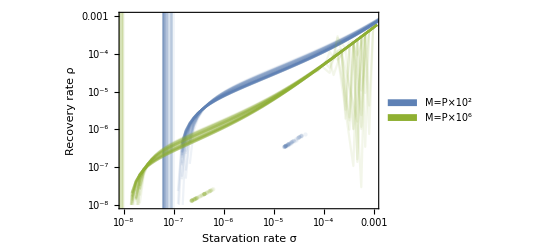

```mathematica
DataHopfPlot=Legended[Show[{
SM,
LM
}],Placed[SwatchLegend[{ColorData[97,1],ColorData[97,3]},{"M=P×10^2","M=P×10^6"},LegendMarkers->"Bubble"],{0.88,0.15}]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf"}],DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf